# Absorption Coefficient

```mathematica
a0GaN:= Quantity[2×10^5,"Centimeter^(-1)"]
a0AlN:= Quantity[1×10^5,"Centimeter^(-1)"]
E0:=Quantity[6.424,"eV"]
AlN:=Quantity[6.28, "eV"]
GaN:=Quantity[3.44, "eV"]
AlContent:= 0.72
a0:= a0AlN *AlContent+ a0GaN*(1-AlContent)
EG:=AlN×(AlContent)+GaN(1-AlContent)

a:= a0 × √((E0-EG)/EG)
```

# Graphing

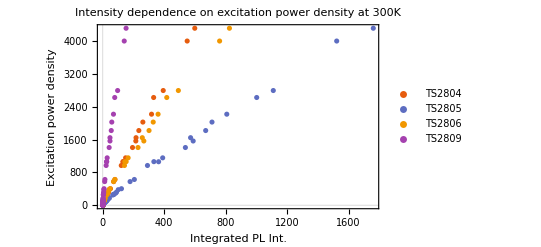

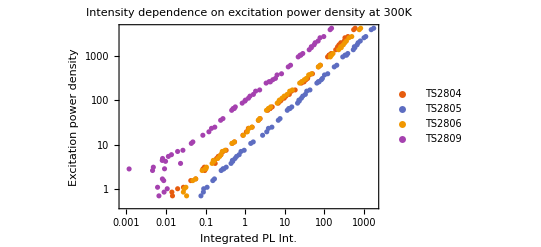

```mathematica
(*t := Import["TS2804.txt","Table"]
ListPlot[t,PlotRange-> Full, PlotLegends->{TS2804}, PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Excitation power density",20],Style["Integrated  PL Int.",20]},
PlotTheme->"Scientific"]*)
s:=N[Import["/Users/ba/Documents/TS2804 swap.txt","Table"]]
t:=N[Import["/Users/ba/Documents/TS2805 swap.txt","Table"]]
v:=N[Import["/Users/ba/Documents/TS2806 swap.txt","Table"]]
w:=N[Import["/Users/ba/Documents/TS2809 swap.txt","Table"]]
ListPlot[{s,t,v,w},PlotRange-> Full, PlotLegends->{TS2804 , TS2805, TS2806, TS2809}, PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Integrated  PL Int.",20],Style["Excitation power density",20]},
PlotTheme->"Scientific"]
ListLogLogPlot[{s,t,v,w},PlotRange-> Full, PlotLegends->{TS2804 , TS2805, TS2806, TS2809}, PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Integrated  PL Int.",20],Style["Excitation power density",20]},
PlotTheme->"Scientific"]
```

```mathematica
Clear[x,r]
s1 :=ArrayReshape[s,{61,2}] //N
t1 :=ArrayReshape[t,{61,2}] //N
v1 :=ArrayReshape[v,{61,2}] //N
w1 :=ArrayReshape[w,{61,2}] //N
l1:=s1[[All,2]]*x*(1-r)/(QuantityMagnitude[E0])*6.241509*10^21
l2:=t1[[All,2]]*x*(1-r)/(QuantityMagnitude[E0])*6.241509*10^21
l3:=v1[[All,2]]*x*(1-r)/(QuantityMagnitude[E0])*6.241509*10^21
l4:=w1[[All,2]]*x*(1-r)/(QuantityMagnitude[E0])*6.241509*10^21
o1:=s1[[All,1]]
o2:=t1[[All,1]]
o3:=v1[[All,1]]
o4:=w1[[All,1]]
m1:= Sort[Transpose[{o1,l1}]]
m2:=  Sort[Transpose[{o2,l2}]]
m3:=  Sort[Transpose[{o3,l3}]]
m4:=  Sort[Transpose[{o4,l4}]]

(*Manipulate[ListPlot[{m1[[1 ;; i]] /.i->I /.x-> α  /.r->R,m2[[1 ;; i]] /.i->I/.x-> α  /.r->R,m3[[1 ;; i]]/.i->I /.x-> α  /.r->R,m4[[1 ;; i]]/.i->I /.x-> α  /.r->R},PlotRange-> Full, PlotLegends->{TS2804 , TS2805, TS2806, TS2809}, PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Integrated  PL Int.",20],Style["Generationsrate",20]},
PlotTheme->"Scientific"],{α, 1*10^4, 1*10^8},{R, 0.1,1.0},{I,1,61,1}]*)

Manipulate[{ListPlot[{N[m1[[1 ;; i]]],N[m2[[1 ;; i]]],N[m3[[1 ;; i]]],N[m4[[1 ;; i]]]}  /.x-> α  /.r->R,PlotRange-> Full, PlotLegends->{TS2804 , TS2805, TS2806, TS2809}, PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Integrated  PL Int.",20],Style["Generationsrate",20]},
PlotTheme->"Scientific"],ListLogLogPlot[{N[m1[[1 ;; i]]],N[m2[[1 ;; i]]],N[m3[[1 ;; i]]],N[m4[[1 ;; i]]]}  /.x-> α  /.r->R,PlotRange-> Full, PlotLegends->{TS2804 , TS2805, TS2806, TS2809}, PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Integrated  PL Int.",20],Style["Generationsrate",20]},
PlotTheme->"Scientific"]},{α, 1*10^4, 1*10^8},{R, 0.1,1.0},{i,1,61,1}]
```

# Data Fitting

```mathematica
x:=1*10^5
r:=0.20
fit1 :=FindFit[m1[[ ;;i,All]],z1*√y+ z2 * y, {z1,z2},y]
fit2 :=FindFit[m2[[ ;;i,All]],z1*√y+ z2 * y, {z1,z2},y]
fit3 :=FindFit[m3[[ ;;i,All]],z1*√y+ z2 * y, {z1,z2},y]
fit4:=FindFit[m4[[ ;;i,All]],z1*√y+ z2 * y, {z1,z2},y]

a1:=(z1/.fit1)
a2:=(z2/.fit1)
b1:=(z1/.fit2)
b2:=(z2/.fit2)
c1:=(z1/.fit3)
c2:=(z2/.fit3)
d1:=(z1/.fit4)
d2:=(z2/.fit4)



Result1:=Solve[a1/√a2*B1 + B1^2 == m1[[j,2]],B1]
Result2:=Solve[b1/√b2*B2 + B2^2 == m2[[j,2]],B2]
Result3:=Solve[c1/√c2*B3 + B3^2 == m3[[j,2]],B3]
Result4:=Solve[d1/√d2*B4 + B4^2 == m4[[j,2]],B4]

Bn1:=B1/.Result1[[2,1]]
Bn2:=B2/.Result2[[2,1]]
Bn3:=B3/.Result3[[2,1]]
Bn4:=B4/.Result4[[2,1]]

IQE1 := Bn1^2/m1[[j,2]]
IQE2 := Bn2^2/m2[[j,2]]
IQE3 := Bn3^2/m3[[j,2]]
IQE4 := Bn4^2/m4[[j,2]]

Off[Part::span]
Off[FindFit::fitd]
Off[ReplaceAll::reps]
Off[Part::pkspec1]

(*Manipulate[{IQE1 /.i ->I /.j->J,IQE2 /.i ->I /.j->J,IQE3 /.i ->I /.j->J,IQE4 /.i ->I /.j->J,Show[ListPlot[{m1[[1 ;; i]],m2[[1 ;; i]],m3[[1 ;; i]],m4[[1 ;; i]]}/.i ->I /.j->J,PlotRange-> Automatic, PlotLegends->{TS2804 swap}],Plot[ { a1*√p+a2*p,b1*√p+b2*p, c1*√p+c2*p,d1*√p+d2*p}/.i-> I /.j->J ,{p,0,600},PlotRange->Automatic]]},{{J,10,"Messpunkt"},1,60,1},{{I,50,"Anzahl Messdaten"},1,60,1}]*)



Manipulate[
Show[ListPlot[{m1[[1 ;; I]],m2[[1 ;; I]],m3[[1 ;;I]],m4[[1 ;; I]]},PlotLegends->{TS2804 , TS2805, TS2806, TS2809}],Plot[ { a1*√p+a2*p,b1*√p+b2*p, c1*√p+c2*p,d1*√p+d2*p}/.i-> I /.j->J ,{p,0,600},PlotRange->Automatic]] ,{{I,50,"Anzahl Messdaten"},1,60,1},SynchronousUpdating->False,AppearanceElements->All]
Manipulate[{IQE1, IQE2, IQE3, IQE4 }/.i ->I /.j->J ,{{J,10,"Messpunkt"},1,60,1},{{I,50,"Anzahl Messdaten"},1,60,1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
x:=1*10^5
r:=0.20
ParallelEvaluate[FindFit[m1[[ 1;;30,All]],z1*√y+ z2 * y, {z1,z2},y]]
```

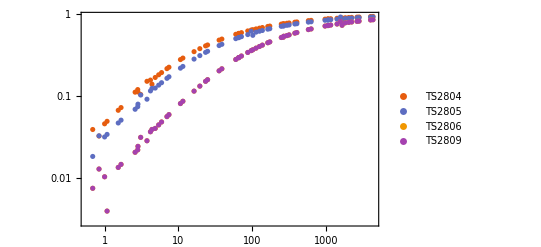

```mathematica
x:=1*10^5
r:=0.20


fit1 :=FindFit[m1[[ 10;;50,All]],z1*√y+ z2 * y, {z1,z2},y] 
fit2 :=FindFit[m2[[ 10;;50,All]],z1*√y+ z2 * y, {z1,z2},y]
fit3 :=FindFit[m3[[ 10;;50,All]],z1*√y+ z2 * y, {z1,z2},y]
fit4:=FindFit[m4[[10 ;;50,All]],z1*√y+ z2 * y, {z1,z2},y]



a1:=(z1/.fit1)
a2:=(z2/.fit1)
b1:=(z1/.fit2)
b2:=(z2/.fit2)
c1:=(z1/.fit3)
c2:=(z2/.fit3)
d1:=(z1/.fit4)
d2:=(z2/.fit4)



Erg1:=Table[Solve[a1/√a2*B1 + B1^2 == m1[[j,2]],B1],{j,1,61,1}] 
Erg2:=Table[Solve[b1/√b2*B2 + B2^2 == m2[[j,2]],B2],{j,1,61,1}]
Erg3:=Table[Solve[c1/√c2*B3 + B3^2 == m3[[j,2]],B3],{j,1,61,1}]
Erg4:=Table[Solve[d1/√d2*B4 + B4^2 == m4[[j,2]],B4],,{j,1,61,1}]



a11:=B1/.Erg1[[;;,2]]
a12:=B2/.Erg2[[;;,2]]
a13:=B3/.Erg3[[;;,2]]
a14:=B4/.Erg4[[;;,2]]




IQE1Tab := a11[[;;]]^2/m1[[;;,2]]
IQE2Tab := a12[[;;]]^2/m1[[;;,2]]
IQE3Tab := a13[[;;]]^2/m1[[;;,2]]
IQE4Tab:= a14[[;;]]^2/m1[[;;,2]]




snew:=Sort[s[[;;,2]]]

t11:=Transpose[{snew,IQE1Tab}]
t12:=Transpose[{snew,IQE2Tab}]
t13:=Transpose[{snew,IQE3Tab}]
t14:=Transpose[{snew,IQE3Tab}]


ListLogLogPlot[{t11,t12,t13,t14},PlotLegends->{TS2804 , TS2805, TS2806, TS2809},PlotRange->Full, PlotTheme->Scientific]
```

```mathematica
IQE1Tab := Table[ParB1^2/m1[[j,2]],{j,1,61,1}]
```